# 初心者用Mathematica簡易マニュアル

Version 12 で確認

## 最初に

まず覚えることは、ノートブックの開き方と、式の評価はエンターキーもしくはシフトキーとリターンキーを同時に押すことにより行われること。

## 数字

小数点のない3や4/9やSin[6]は「記号的に」評価される。

```mathematica
4/9+7/9
```

11/9

3.1415は有限精度として評価される。

N[]で倍精度実数に変換できる．

```mathematica
N[4/9]
```

0.444444

```mathematica
FullForm[%]
```

0.444444

N[]で計算桁数を指定できる。

```mathematica
N[4/9,50]
```

0.44444444444444444444444444444444444444444444444444

## 評価(計算：Evaluation)

評価したい式を選んでテンキーの「Enter」もしくはシフトキー+「Return]

## 変数や関数の名前

変数や関数は文字で始まる。変数はそれが評価された時点で定義される。

Sin[x], Abcd, Pi

## 変数の初期化と消去

初期化： a=. または Clear[a]

消去（変数そのものを削除）：Remove[a]

## 「；」による表示の抑止

```mathematica
list={a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
list={a,b,c,d,e};
```

## 特殊な定数

E（ネーピアの数）, Pi（円周率）, EulerGamma（オイラー定数）, 
C（積分定数）など

```mathematica
?E
```

```mathematica
?Pi
```

```mathematica
?EulerGamma
```

```mathematica
?C
```

## 代入

直ちに評価される　＝

```mathematica
a=2
```

2

グラフィクスなど、実際の計算時に評価される　:＝
「:=」は関数の定義やパラメータの指定に便利。

```mathematica
b:=2
```

## 四則演算

+,-,*,/　　　：足し算、引き算、かけ算、割り算

「*」はスペースでも良い。

次のような場合も積と解釈される。

Sin[x]Cos[x]

7x

## 関数の定義

Mathematicaであらかじめて定義された関数や命令は大文字で始まる。「引き数」は[]で囲む。

Sin[x],Do[.....], ..., etc

ユーザー定義の関数（大文字で初めてもよい）

```mathematica
func1[x_]:=Sin[2*x]
```

アンダースコアは「_」はスカラーの引き数をあらわす。

```mathematica
func2[x_,y_]:=Sin[2*x]Cos[y]
```

アンダースコア２つは「__」はリストの引き数をあらわす。

```mathematica
func2[x__]:=x/Length[x]
```

## 配列（リスト）

```mathematica
a={{1,2},{3,4},{5,6}}
```

{{1,2},{3,4},{5,6}}

リストの長さ

```mathematica
Length[a]
```

3

```mathematica
?Dimensions
```

リストの長さ(2)

```mathematica
Dimensions[a]
```

{3,2}

配列の要素は[[]]で指定する

```mathematica
a[[1]]
```

{1,2}

```mathematica
a[[3,2]]
```

6

## 配列の生成

Table関数を使う方法がある。開始を省略すると、添字は１から始まる。

```mathematica
Table[Sin[j],{j,3}]
```

{Sin[1],Sin[2],Sin[3]}

ループは外側から変化する。

```mathematica
Table[j*Sin[k],{j,2,4},{k,2}]
```

{{2 Sin[1],2 Sin[2]},{3 Sin[1],3 Sin[2]},{4 Sin[1],4 Sin[2]}}

## 行列積（内積）「.」

```mathematica
a={{a0,b0},{c0,d0}}
```

{{a0,b0},{c0,d0}}

```mathematica
v={v1,v2}
```

{v1,v2}

```mathematica
a.v
```

{a0 v1+b0 v2,c0 v1+d0 v2}

```mathematica
v.v
```

v1^2+v2^2

Mathematicaでは行ベクトルと列ベクトルを区別しない。

```mathematica
v.a
```

{a0 v1+c0 v2,b0 v1+d0 v2}

## くり返しの例

```mathematica
x=1/5
```

1/5

```mathematica
Do[x=x^2;Print[Sin[x]],{i,5}]
```

Sin[1/25]

Sin[1/625]

Sin[1/390625]

Sin[1/152587890625]

Sin[1/23283064365386962890625]

くり返す命令は「;」で区切る。くり返しの範囲「{...}」は「,」で区切る。

## 関数のプロット

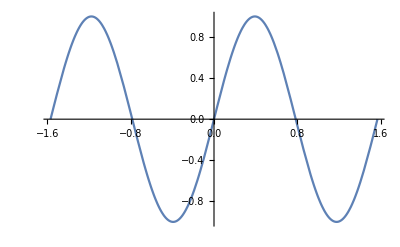

```mathematica
Plot[Sin[4x],{x,-Pi/2,Pi/2}]
```

```mathematica
Plot3D[Sin[Pi x]Sin[Pi y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

## グラフの重ね合わせ

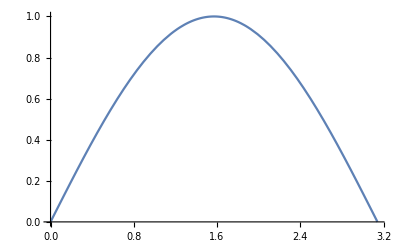

```mathematica
g1=Plot[Sin[x],{x,0,Pi}]
```

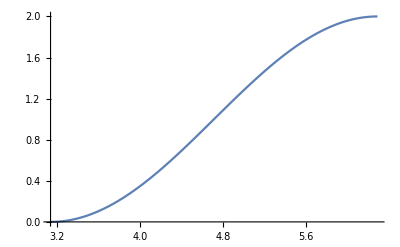

```mathematica
g2=Plot[1+Cos[x],{x,Pi,2Pi}]
```

変数にグラフィクスオブジェクトをセットすることができる。
さらにそれらを使ってグラフの合成ができる。

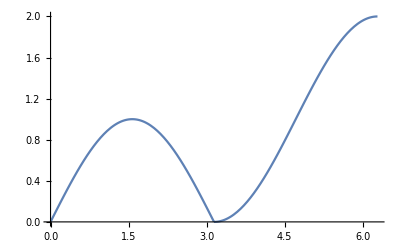

```mathematica
Show[g1,g2,PlotRange->All]
```

## リストのプロット

1次元リスト

```mathematica
a=Table[Sin[Pi j / 10],{j,0,10}]
```

{0,1/4 (-1+√5),√(5/8-(√5)/8),1/4 (1+√5),√(5/8+(√5)/8),1,√(5/8+(√5)/8),1/4 (1+√5),√(5/8-(√5)/8),1/4 (-1+√5),0}

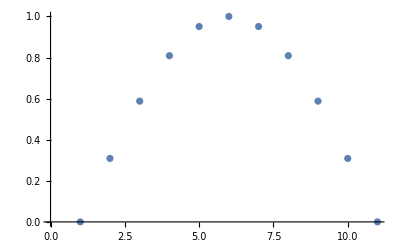

```mathematica
ListPlot[a]
```

"Joined->True"で点を順番につなぐ

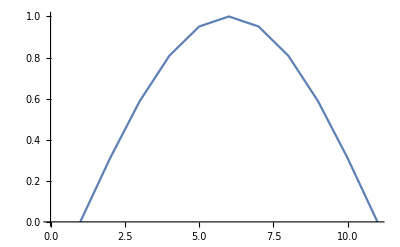

```mathematica
ListPlot[a,Joined->True]
```

２次元リスト

```mathematica
a=Table[{Cos[2Pi j / 10],Sin[2Pi j / 10]},{j,0,10}]
```

{{1,0},{1/4 (1+√5),√(5/8-(√5)/8)},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (1-√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{-1,0},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (1-√5),-√(5/8+(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)},{1/4 (1+√5),-√(5/8-(√5)/8)},{1,0}}

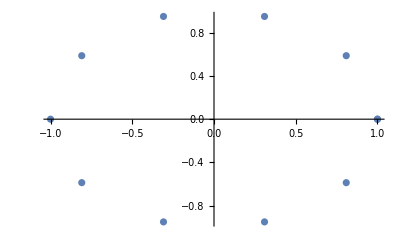

```mathematica
ListPlot[a]
```

"Joined->True"で点を順番につなぐ

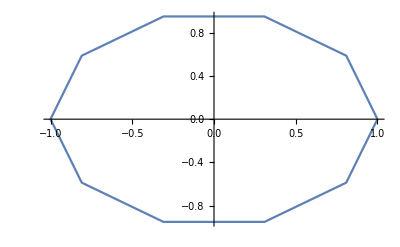

```mathematica
ListPlot[a,Joined->True]
```

## 和

級数

```mathematica
Sum[Sin[n],{n,5}]
```

Sin[1]+Sin[2]+Sin[3]+Sin[4]+Sin[5]

```mathematica
Sum[1/n^2,{n,Infinity}]
```

π^2/6

配列（リスト）の成分の和

```mathematica
a=Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Plus@@a
```

55

## リストの操作

変数を初期化する

```mathematica
Clear[a,b,c,d,e]
```

リストの定義

```mathematica
list={a,b,c,d,e}
```

{a,b,c,d,e}

左シフト

```mathematica
Table[RotateLeft[list,i],{i,0,5}]
```

{{a,b,c,d,e},{b,c,d,e,a},{c,d,e,a,b},{d,e,a,b,c},{e,a,b,c,d},{a,b,c,d,e}}

右シフト

```mathematica
Table[RotateRight[list,i],{i,0,5}]
```

{{a,b,c,d,e},{e,a,b,c,d},{d,e,a,b,c},{c,d,e,a,b},{b,c,d,e,a},{a,b,c,d,e}}

```mathematica
a=Table[{Pi(i-1)/10,Sin[Pi(i-1)/10]},{i,11}]
```

{{0,0},{π/10,1/4 (-1+√5)},{π/5,√(5/8-(√5)/8)},{(3 π)/10,1/4 (1+√5)},{(2 π)/5,√(5/8+(√5)/8)},{π/2,1},{(3 π)/5,√(5/8+(√5)/8)},{(7 π)/10,1/4 (1+√5)},{(4 π)/5,√(5/8-(√5)/8)},{(9 π)/10,1/4 (-1+√5)},{π,0}}

```mathematica
Length[a]
```

11

偶数番目の抽出(1)：indexによる方法

```mathematica
Table[a[[i]],{i,2,11,2}]
```

{{π/10,1/4 (-1+√5)},{(3 π)/10,1/4 (1+√5)},{π/2,1},{(7 π)/10,1/4 (1+√5)},{(9 π)/10,1/4 (-1+√5)}}

偶数番目の抽出(2)：写像による方法
Mathematicaでよく使われるテクニック

変域を定義

```mathematica
n=Table[i,{i,2,11,2}]
```

{2,4,6,8,10}

nを変域とする写像

```mathematica
Map[a[[#]]&,n]
```

{{π/10,1/4 (-1+√5)},{(3 π)/10,1/4 (1+√5)},{π/2,1},{(7 π)/10,1/4 (1+√5)},{(9 π)/10,1/4 (-1+√5)}}

2021, chibaf